## MICA: Measurement, Instrumentation, Control and Analysis

## Measure Sound Speed from Pulse

#### Ian Hunter, MIT, 12 February 2026

#### Objectives

We use the Digilent Discovery instrument to measure the sound signal recorded by a MEMS microphone at about 50, 100, 150, 200 and 250 mm above a small voice coil type speaker. The speaker is driven from the Digilent Discovery digital to analog convertor (DAC) (waveform channel 1 out) which outputs a 10 μs, 5 V pulse every 10 ms.
100 such sound signals are averaged and stored in a CSV file at each of the 5 positions. These files is then imported in to Mathematica. The acoustic pulse response signals are then analyzed to measure the delay between the speaker and the microphone. The speed of sound in air is estimated both manually and via least squares fitting. The attenuation of the sound pulse with distance is also measured.

#### Key Concepts

MEMS Microphone, Voice Coil Speaker, Analog to Digital Converter (ADC), Digital to Analog Converter (DAC), Dynamic Range, 14 bit Dynamic Range, Buffer, Waveform Generator, Pulse Input, Pulse Repetition Rate, Pulse Amplitude, Power Supply, Oscilloscope, Differential Inputs, Least Squares Model Fitting, Linear Model, Power Function, Parameter Estimation, Uncertainty, Speed of Sound, Attenuation.

#### OnShape CAD model

The CAD model of this system is available here: https://cad.onshape.com/documents/1bba7d25b119e80d3fd73296/w/8ea1ce073f7cc126462f63fc/e/907417eb1437adcaf53f4f24?renderMode=0&uiState=698a7fccfa49260d1348e098

#### MEMS Microphone

-Graphics-    -Graphics-

We use a micro-electro-mechanical system (MEMS) microphone made by Knowles (model SPH8878LR5H-1 ; https://cdn.sparkfun.com/assets/0/5/8/b/1/SPH8878LR5H-1_Lovato_DS.pdf ) and available together with an operational amplifier (Op Amp) (OPA344) on a printed circuit board (PCB) from Sparkfun Electronics.

	•	Supply Voltage: 2.3-3.6V
	•	Average Current Consumption: 265µA
	•	Frequency Range: 7Hz-36kHz
	•	Signal-to-Noise Ratio: 66dBV/Pa
	•	Sensitivity: -44dBV/Pa (Single-Ended Mode)
	•	-3dB Roll Off at 7Hz / +3dB Flatness at 36kHz
	•	Acoustic Overload Point: 134dB SPL
	•	OPA344 provides 600Ω output impedance

Note that when there is no sound the MEMS mic outputs 0.5 x power supply voltage. We will drive it with 3 V and so the output with no sound will be 1.5 V.

#### Speaker

We use a small 4 Ω or 8 Ω voice coil (Lorentz force) speaker.

#### Wiring

Connect:
1. speaker input (Red or Black (see note below)) to Digilent W1 (signal generator) (Yellow) output
2. speaker input (Black or Red (see note below)) to Digilent ground (Black)
3. Digilent W1 (Yellow) output also to Digilent Scope 1 +ve (Orange) input (I will show you in class how to join 2 wires)
4. Digilent Scope 1 -ve (Range/White) input to any Digilent ground (Black)
5. microphone +ve power input (VCC) to the Digilent positive power supply V+ (Red) output which will be set to +3 V
6. microphone ground (GND) to any of the Digilent grounds (Black)
7. microphone output (AUD) to the Digilent Scope 2 +ve input (Blue)
8. Digilent Scope 2 -ve input (Blue/White) to any Digilent ground (Black)

#### Experimental Setup

We need to make sure that the Digilent is using its 32k input buffer. Click on the Discovery 3 C SN:... button on the bottom of the Digilent Window.

and select option 2:

We need 3 V to drive the microphone and associated audio amplifier.

We need to generate 10 μs duration pulses at 100 Hz. When the Symmetry is set to 50% (the default) then we get a pulse which is 5 ms long. So to get a 10 μs duration pulse we need to set the symmetry to 0.1 %.

Here is a screen shot when the microphone is 100 mm from the speaker. 
Note: If your microphone output (Blue line) starts negative then swap your speaker wires.
I have changed the Channel 1 default line color from Orange to Red (click on gear icon if you feel the aesthetic need to do this).
We have expanded the Time box to show the sampling rate and set the Time Base to 100 us/div (Rate will probably be 14.286 MHz) and we want to turn on averaging (use 100). 
Set Time base Position to be 400 us. This will move the speaker input pulse (Red line below) over by 100 us so that you can more clearly see the pulse start.
Set Channel 1 Range to 2 V/div
Set the Channel 2 Offset to -1.5 V (because the mic output is 1.5 V for no acoustic signal).
Set the trigger Source to Wavegen C1 (we might as well trigger on the signal generator pulse rather than try to trigger on the measured pulse input).
Set the Channel 2 Range to be some where between 500 mV/div and 50 mV/div depending on the peak to peak voltage from the mic. Note that as you move away from the mic the sound decays so you will need to boost the sensitivity of the Voltage axis range (e.g.,  perhaps start with 100 mV/div at the 50 mm mic position and end up with 20 mV/div at the 250 mm mic position).
Remember to save an averaged pulse response at each of the 5 positions (click on Export at the far left of the screen).
It helps to run the averaging a few times before saving to get a fairly straight initial “flat” region as in the signal shown below. Call your Exported waveforms “SoundData50mm”, “SoundData100mm”, etc.

#### Run Experiment

The vertical column of the setup has notches every 50 mm corresponding to the vertical position between the speaker cone and microphone. Note that the first notch (0 mm) cannot be used. Measure the microphone pulse response (average of 100 repetitions) at 50, 100, 150, 200 and 250 mm speaker to microphone distances. As mentioned above save (Export)  the signal at each position and use file names such as SoundData50mm, SoundData100mm etc.

#### Import the 5 Acoustic Signals

We have to first check to see at what row the data starts.

```mathematica
"■"; 
path="C:\\Users\\ariel\\OneDrive\\Documents\\2.131 Experiments"; (* change this to your path name *)
data=Import[path <>"/SoundData50mm.csv" ];
```

Lets look at the first 30 rows:

```mathematica
"■"; data[[1;;30]] (* just display rows 1 to 30 *)
```

{{#Digilent WaveForms Oscilloscope Acquisition},{#Device Name: Discovery3},{#Serial Number: SN:210415BE893B},{#Date Time: 2026-02-11 14:40:52.468.562.720},{#Sample rate: 2.5e+07Hz},{#Samples: 32768},{#Trigger: Source: Wavegen C1 Condition: Rising},{#Average: 100},{#Channel 1: Range: 2 V/div Offset: 0 V Sample Mode: Average},{#Channel 2: Range: 100 mV/div Offset: -1.5 V Sample Mode: Average},{#Wavegen Channel 1: Running},{#Mode: Simple},{#Type: Pulse},{#Frequency: 100 Hz},{#Period: 10 ms},{#Amplitude: 5 V},{#Offset: 0 V},{#Symmetry: 0.1 %},{#Phase: 0 °},{#Power Supplies: ON},{#Positive Supply: ON},{#Voltage: 3 V Readback: 3.003983517 V},{#Negative Supply: OFF},{#Voltage: -1 V},{Time (s),Channel 1 (V),Channel 2 (V)},{-0.00025536,0.0265452,1.50556},{-0.00025532,0.0259342,1.50554},{-0.00025528,0.0259971,1.50561},{-0.00025524,0.026725,1.50562},{-0.0002552,0.0265183,1.50563}}

We can see that the data triplets {time,Ch1,Ch2} start at row 26 (count back from row 30):
So now we can import all the Ch2 (i.e., microphone) measurements:

```mathematica
"■"; row=26; (* row at which the first sample occurs (yours may be slighlty different (check to see)) *)
data=Import[path <>"/SoundData50mm.csv" ];
data50mm=data[[row;;All,3]]; (* note that we select column 3 *)
data=Import[path <>"/SoundData100mm.csv" ];
data100mm=data[[row;;All,3]];(* note that we select column 3 *)
data=Import[path <>"/SoundData150mm.csv" ];
data150mm=data[[row;;All,3]];(* note that we select column 3 *)
data=Import[path <>"/SoundData200mm.csv" ];
data200mm=data[[row;;All,3]];(* note that we select column 3 *)
data=Import[path <>"/SoundData250mm.csv" ];
data250mm=data[[row;;All,3]];(* note that we select column 3 *)
t=data[[row;;All,1]]; (* note that we select column 1: the sample times should be the same for all 5 data sets *)
n=Length[t]
```

32768

There should be 2^15 = 32768 samples in each of the 5 signals. This is the Digilent Discovery 3 max buffer length (Option 2 selected before).

We can find the time in seconds between each sample by:

```mathematica
"■"; Δt=t[[2]]-t[[1]]
```

4.×10^-8

So in nano-seconds this is:

```mathematica
"■"; 10^9 Δt
```

40.

So the sampling rate in Hz is:

```mathematica
"■"; 1/Δt
```

2.5×10^7

#### Plot the Acoustic Signals

```mathematica
"■"; ListLinePlot[{t,data50mm}ᵀ,PlotRange->All,PlotStyle->Red,ImageSize->600]
```

-Graphics-

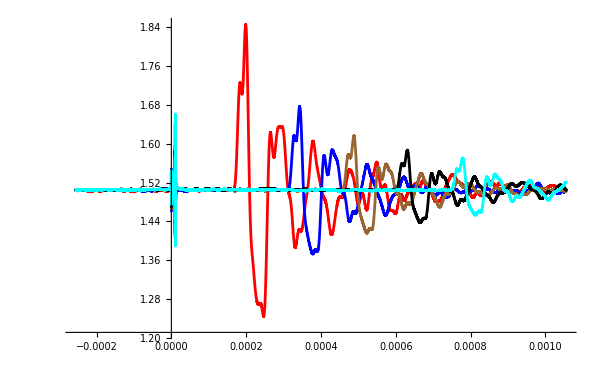

```mathematica
"■"; ListLinePlot[{{t,data50mm}ᵀ,{t,data100mm}ᵀ,{t,data150mm}ᵀ,{t,data200mm}ᵀ,{t,data250mm}ᵀ},
PlotStyle->{Red,Blue,Brown,Black,Cyan},PlotRange->All,ImageSize->600]
```

We notice from this plot that the first and largest peak shifts to the right as the microphone to speaker distance increases. We also note that the amplitude of this pulse response decreases with increased distance. In other words sound intensity “rolls off” with distance from the source. We can speculate whether this attenuation of the sound signal with distance increases linearly or nonlinearly. And if it is nonlinear then what sort of nonlinear function of distance is it.

#### Initial Signal Processing

We have a 1.5 V offset caused by the microphone (i.e., 0 acoustic input corresponds to 1.5 V mic output).  
Lets set this 1.5 V offset to 0:

```mathematica
"■"; 
sound50mm=data50mm-1.5;
sound100mm=data100mm-1.5;
sound150mm=data150mm-1.5;
sound200mm=data200mm-1.5;
sound250mm=data250mm-1.5;
```

Now lets re-plot but this time with axis labels.

```mathematica
"■"; ListLinePlot[{{10^6 t,sound50mm}ᵀ,{10^6 t,sound100mm}ᵀ,{10^6 t,sound150mm}ᵀ,{10^6 t,sound200mm}ᵀ,{10^6 t,sound250mm}ᵀ},
PlotStyle->{Red,Blue,Brown,Black,Cyan},GridLines->Automatic,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (μs)","Amplitude (V)"},AspectRatio->0.5,PlotLabel->"Acoustic Pulse Responses",PlotRange->All,ImageSize->600]
```

-Graphics-

#### Delay Estimate

We can manually estimate the delay between the 50 mm and 100 mm microphone positions by using the function Manipulate[].
Move the sliders until the red (50mm) signals initial peak overlays the blue (100mm) one (click on + button on right side of slider to get fine adjustment):

```mathematica
"■"; Δi=0;
Manipulate[
Δi=Δii;
ListLinePlot[{{10^6 t[[Δi;;All]],sound50mm[[1;;n-Δi+1]]}ᵀ,{10^6 t[[Δi;;All]],
(α sound100mm[[Δi;;All]])}ᵀ},PlotRange->{{0,All},All},
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->{Red,Blue},LabelStyle->{14,Black},PlotLabel->"Acoustic Response (50 mm Red, 100 mm Blue)",
FrameLabel->{"Time (μs)","Amplitude (V)"},AspectRatio->0.5,ImageSize->600],
{{α,1},1,3.0,Appearance->"Labeled"},
{{Δii,1,"Δi"},1,4500,1,Appearance->"Labeled"}]
```

Lets record the number of samples needed to shift the acoustic pulse signal at 50 mm so that it overlays the initial peak of the 100 mm signal.

So the shift in seconds is:

```mathematica
"■"; Δi Δt
```

0

The distance between the microphone at the 50 mm position and the 100 mm position is 50 mm. So the speed of sound should be:

```mathematica
"■"; (0.05 Quantity[, "Meters"])/(Δi Δt Quantity[, "Seconds"])
```

343.69 m/s

Mathematica allows us to access a huge data base of material properties, constants and physical equations. 
Lets ask for the speed of sound in air at 24 deg C (the temperature of my basement lab):

```mathematica
"■"; soundSpeedAirAt24degC=ThermodynamicData["Air", "SoundSpeed", {"Temperature" -> Quantity[24, "DegreesCelsius"]}]
```

345.672 m/s

So the % difference between this value and our measurement is:

```mathematica
"■"; Abs[100((0.05 Quantity[, "Meters"])/(Δi Δt Quantity[, "Seconds"])-soundSpeedAirAt24degC)/soundSpeedAirAt24degC]
```

0.244191

This is fairly close given the uncertainty of our “notched” microphone positioning system. But can we do better by using all 5 of our signals?

#### Determine Delay Algorithmically

We can determine the index of the peak positive value using:

```mathematica
"■"; 
peakIndex50mm=Ordering[sound50mm[[7500;;n]],-1][[1]];
peakIndex100mm=Ordering[sound100mm[[7500;;n]],-1][[1]];
peakIndex150mm=Ordering[sound150mm[[7500;;n]],-1][[1]];
peakIndex200mm=Ordering[sound200mm[[7500;;n]],-1][[1]];
peakIndex250mm=Ordering[sound250mm[[7500;;n]],-1][[1]];
```

Note that in order to avoid the initial spikes in the data caused by the current pulse sent to the speaker being picked up by the microphone we omitted the first 7500 samples (i.e., 300 μs).

Lets create a 5 element list of the times corresponding to the index of the first peak:

```mathematica
"■"; delay={Δt peakIndex50mm,Δt peakIndex100mm,Δt peakIndex150mm,Δt peakIndex200mm,Δt peakIndex250mm};
```

and a list containing the distances in m:

```mathematica
"■"; distance={0.05,0.10,0.15,0.20,0.25};
```

#### Plot Delays

Lets now plot these

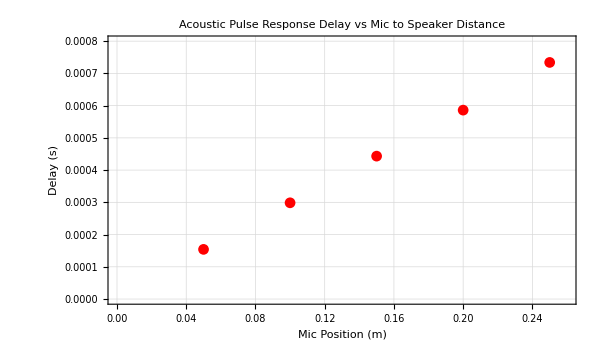

```mathematica
"■"; ListPlot[{distance,delay}ᵀ,
PlotRange->{{0.0,0.26},{0.0,0.0008}},PlotStyle->Red,GridLines->Automatic,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Mic Position (m)","Delay (s)"},AspectRatio->0.6,PlotLabel->"Acoustic Pulse Response Delay vs Mic to Speaker Distance",PlotRange->All,ImageSize->600]
```

The data appear to be linear. 
Lets fit a straight line to the data using least squares just to check and also to determine the slope and intercept:

```mathematica
"■"; lm=LinearModelFit[{distance,delay}ᵀ,dist,dist]
```

FittedModel[…]

The R^2 value is very high:

```mathematica
"■"; lm["RSquared"]
```

0.999974

and the parameters (slope and intercept) are given by:

```mathematica
"■"; par=lm["BestFitParameters"]
```

{9.004×10^-6,0.00289464}

Lets re-plot the data together with the fitted model (and improved fonts):

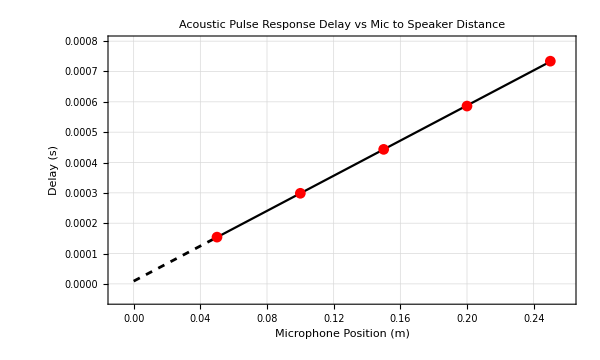

```mathematica
"■"; Show[
Plot[lm[dist],{dist,0.05,0.25},PlotRange->{{-0.01,0.26},{-0.00005,0.0008}},PlotStyle->Black,PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Acoustic Pulse Response Delay vs Mic to Speaker Distance",FontFamily->"Times",FontSize->18,Bold,Black],
FrameLabel->{Style["Microphone Position (m)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Delay (s)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->600],
Plot[lm[dist],{dist,0.0,0.05},PlotStyle->{Black,Dashed}],
ListPlot[{distance,delay}ᵀ,PlotStyle->Red]
]
```

Note the order in which the three plots are plotted. This ordering ensures that the red dots (the data) appear above the black lines. We have also improved the look of the plot by using bold and larger fonts on each axis. This is now a publication quality plot.

What does the slope of this line tell us. Well, its reciprocal is our least squares estimate of the speed of sound!
Lets determine it:

```mathematica
"■"; 1/par[[2]]
```

345.466

```mathematica
"■"; soundSpeedAirAt24degC
```

345.672 m/s

So the % difference between this value and our measurement is:

```mathematica
"■"; 100Abs[(1.0/par[[2]] Quantity[, ("Meters")/("Seconds")]-soundSpeedAirAt24degC)/soundSpeedAirAt24degC]
```

0.0594732

This is remarkably good given the approximate positioning achieved by manually moving the microphone carrier to different notched positions.

#### Sound Attenuation with Distance

Lets determine the amplitude of the positive first peak of the pulse response. The indexes of these peaks are:

```mathematica
"■"; {peakIndex50mm,peakIndex100mm,peakIndex150mm,peakIndex200mm,peakIndex250mm}
```

{3852,7464,11083,14651,18350}

So the sound amplitude at this peak is (we have to add back in the 7500 points we omitted earlier):

```mathematica
"■"; amplitude={sound50mm[[ 7499+peakIndex50mm]],sound100mm[[7499+peakIndex100mm]],sound150mm[[7499+peakIndex150mm]],sound200mm[[7499+peakIndex200mm]],sound250mm[[7499+peakIndex250mm]]}
```

{0.345779,0.176598,0.116053,0.0866199,0.0703578}

Lets plot these sound amplitude vs distance from speaker:

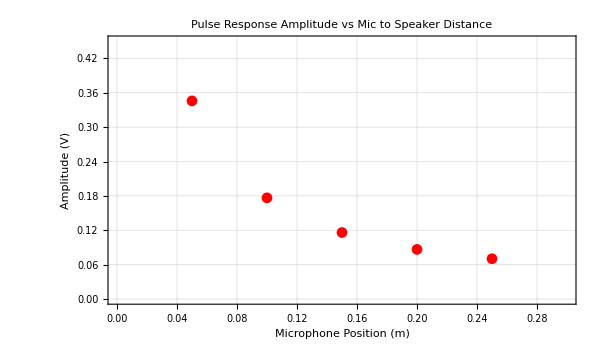

```mathematica
"■"; ListPlot[{distance,amplitude}ᵀ,PlotStyle->Red,
PlotRange->{{0,0.3},{0,0.45}},PlotStyle->Black,PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Pulse Response Amplitude vs Mic to Speaker Distance",FontFamily->"Times",FontSize->18,Bold,Black],
FrameLabel->{Style["Microphone Position (m)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->600]
```

#### Fit a Power Function

Lets fit a 2 parameter power function to the data. We will use a nonlinear minimization technique for this. The NonlinearModelFit[]  algorithm finds the parameters, a and b,  that minimize the sum of squared vertical deviations between model and data):

```mathematica
Clear[a,b]
```

```mathematica
"■"; nlm2=NonlinearModelFit[{distance,amplitude}ᵀ,a dist^b,{a,b},dist]
```

FittedModel[…]

```mathematica
"■"; nlm2["RSquared"]
```

0.99996

The fit is very good.

```mathematica
"■"; nlm2["BestFitParameters"]
```

{a→0.0178827,b→-0.989207}

Notice that the exponent, b, of the fitted power function model is near -1. In other words the sound amplitude rolls off as the inverse of distance.

Lets refit the data but now we fix the exponent at -1. In other words lets fit the model:
amplitude = a/dist

```mathematica
"■"; nlm1=NonlinearModelFit[{distance,amplitude}ᵀ,a dist^-1,a,dist]
```

FittedModel[…]

```mathematica
"■"; nlm1["RSquared"]
```

0.999933

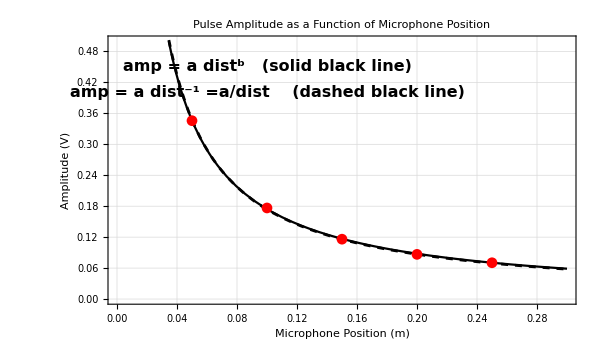

```mathematica
"■"; 
Show[
Plot[nlm2[dist],{dist,0,0.3},PlotRange->{{0,0.3},{0,0.5}},PlotStyle->Black,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Pulse Amplitude as a Function of Microphone Position",FontFamily->"Times",FontSize->18,Bold,Black],
FrameLabel->{Style["Microphone Position (m)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
Epilog->{Text[Style["amp = a dist^b   (solid black line)",FontFamily->"Times",FontSize->16,Bold,Black],{0.1,0.45},{-1,0}],
Text[Style["amp = a dist^-1 =a/dist    (dashed black line)",FontFamily->"Times",FontSize->16,Bold,Black],{0.1,0.4},{-1,0}]},
PlotLabels->None,AspectRatio->0.6,ImageSize->600],
Plot[nlm1[dist],{dist,0,0.3},PlotRange->{{0,0.3},{0,0.7}},PlotStyle->{Black,Dashed}],
ListPlot[{distance, amplitude}ᵀ,PlotStyle->Red]
]
```

We can see that we get a similar fit with by fixing the exponent, b, to -1 rather than letting it be an additional free parameter.